## Initial Values

```mathematica
ρinf=100;
nn=10000;
dρ=ρinf/nn;
```

## Hamiltonian

```mathematica
dρ=0.1;
ρinf=100;
nn=10000;
```

```mathematica
λ=0.85;
```

```mathematica
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
```

```mathematica
Sort[Eigenvalues[H,-100]]
```

{-0.0000578764,0.0000128508,0.0000494927,0.000107556,0.000186029,0.000284547,0.000402969,0.000541233,0.00069931,0.000877183,0.00107484,0.00129228,0.00152951,0.0017865,0.00206327,0.00235982,0.00267613,0.00301222,0.00336808,0.00374371,0.00413911,0.00455429,0.00498923,0.00544394,0.00591842,0.00641267,0.0069267,0.00746049,0.00801405,0.00858738,0.00918047,0.00979334,0.010426,0.0110784,0.0117505,0.0124425,0.0131542,0.0138857,0.0146369,0.0154079,0.0161987,0.0170092,0.0178396,0.0186896,0.0195595,0.0204491,0.0213585,0.0222876,0.0232365,0.0242052,0.0251936,0.0262018,0.0272298,0.0282775,0.029345,0.0304323,0.0315393,0.0326661,0.0338126,0.0349789,0.036165,0.0373708,0.0385964,0.0398418,0.0411069,0.0423918,0.0436964,0.0450208,0.046365,0.0477289,0.0491126,0.0505161,0.0519393,0.0533822,0.054845,0.0563274,0.0578297,0.0593517,0.0608934,0.062455,0.0640362,0.0656372,0.067258,0.0688986,0.0705589,0.0722389,0.0739387,0.0756583,0.0773976,0.0791567,0.0809355,0.0827341,0.0845524,0.0863905,0.0882483,0.0901259,0.0920232,0.0939403,0.0958772,0.0978338}

## Rootfinding Functions

```mathematica
Critical[λ_]:=Module[{H,res},
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
];
```

```mathematica
Critical2[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=consts[[2]];
nn=consts[[3]];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
];
```

```mathematica
CountNegs[list_]:=Module[{neg,i},
neg=0;
For[i=1,list[[i]]<0,i++,
neg++;
];
Return[neg]
]
```

```mathematica
Bisect[F_,x0_,xf_,ϵ_]:=Module[{mid,val,vam,ret},
mid=x0+Abs[x0-xf]/2;
val=F[x0];
vam=F[mid];
If[Abs[vam]>ϵ,
If[val*vam<0,
Return[Bisect[F,x0,mid,ϵ]];,
Return[Bisect[F,mid,xf,ϵ]];
];,
Return[mid];
]
];
```

```mathematica
Bisect2[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,mnegs,vam,ret},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint "<>ToString[mid]];
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
If[lnegs<mnegs||(lnegs==mnegs&&val[[1]]<vam[[1]]),
Return[Bisect2[F,consts,x0,mid,ϵ]];,
Return[Bisect2[F,consts,mid,xf,ϵ]];
];,
Return[mid];
]
];
```

## Using said functions

I found out pretty early on that Critical[0.75] was less than 10^(-3), so I used that to make sure my Bisect recursion was working right. As you can see here, it is.

```mathematica
Bisect[Critical, 0.5,1,10^-3]
```

0.75

```mathematica
Bisect[Critical,0.5,1.5,10^-3]
```

0.75

Because taking 25 eigenvalues sped Critical[] up quite a bit and I knew we were in the neighborhood of the critical value, I went back to my plan of plotting the smallest eigenvalue, below.

```mathematica
Timing[Critical[0.85]]
```

{0.567056,-0.0000114296}

```mathematica
x=Table[{λ,Critical[λ]},{λ,1/2,1,0.025}];
```

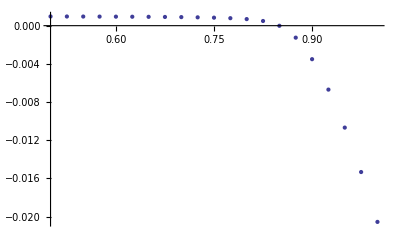

```mathematica
ListPlot[x]
```

This enabled me to narrow down my range for bisect. Result is for ϵ = 10^(-6), because I have no idea what a reasonable ϵ is for this problem.

```mathematica
Bisect[Critical,0.845,0.855,10^-6]
```

0.849609

### Turning it up:

```mathematica
ρinf=1000;
nn=100000;
dρ=ρinf/nn;
```

```mathematica
Timing[Critical[0.85]]
```

{14.2223,-0.000109497}

It’s more expensive now :( Also, that’s a much higher number.

```mathematica
y=Table[{λ,Critical[λ]},{λ,0.8,0.9,0.01}];
```

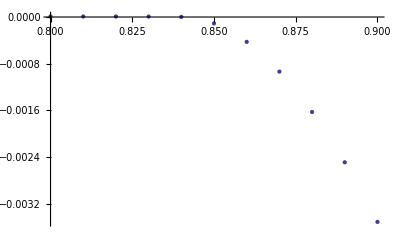

```mathematica
ListPlot[y]
```

Also the critical point seems to have moved a bit.

```mathematica
yy=Table[{λ,Critical[λ]},{λ,0.82,0.85,0.005}];
```

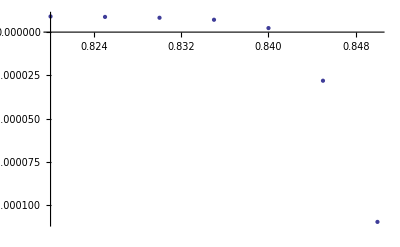

```mathematica
ListPlot[yy]
```

This matrix is I think the last one for which plotting makes sense -- it’s taking two minutes to generate each of these. That said, it also looks like we want to bisect around 0.840.

```mathematica
Bisect[Critical,0.84,0.845,10^-8]
```

0.840884

Cranking up the grid *again*....

```mathematica
ρinf=1000;
nn=1000000;
dρ=ρinf/nn;
```

```mathematica
Bisect[Critical,0.835,0.845,10^-8]
```

0.840859

## Testing accuracy

#### Part 1

```mathematica
Timing[Bisect[Critical,0.84,0.85,10^(-8)]]
```

{17.9235,0.849636}

decrease dρ:

```mathematica
ρinf=100;
nn = 100000;
dρ = ρinf/nn;
```

```mathematica
Timing[Bisect[Critical,0.84,0.85,10^(-8)]]
```

{341.299,0.849608}

```mathematica
ρinf=1000;
nn = 100000;
dρ = ρinf/nn;
```

```mathematica
Timing[Bisect[Critical,0.84,0.85,10^(-8)]]
```

{310.742,0.840884}

```mathematica
ρinf=1000;
nn = 1000000;
dρ = ρinf/nn;
```

```mathematica
Timing[Bisect[Critical,0.835,0.845,10^(-8)]]
```

{2211.03,0.840859}

Improvement by upping ρinf:

```mathematica
0.849636-0.840884
```

0.008752

```mathematica
0.849608-0.840859
```

0.008749

by upping dρ

```mathematica
0.849636-0.84908
```

0.000556

```mathematica
0.840884-0.840859
```

0.000025

```mathematica
ρinf=10000;
nn = 1000000;
dρ = ρinf/nn;
```

```mathematica
Bisect[Critical,0.83,0.845,10^(-8)]
```

0.84002

```mathematica
10000/1000000
```

1/100

### Results

```mathematica
TimingData[min_,max_,step_]:=Module[{i,res},
res={};
For[i=min,i≤max,i=i+step,
Print["Calculating next step"];
res=Append[res,Timing[Bisect2[Critical2,{0.01,i,i/0.01},0.84,0.85,10^(-8)]]];
];
Return[res]
]
```

```mathematica
valtimes=Timeandnumbers=TimingData[100,1500,100];
```

Calculating next step

Calculating next step

Calculating next step

«12 more identical outputs»

```mathematica
valtimes={{18.371306000000004,0.8496356201171874},{36.80777399999988,0.844736328125},{25.82021900000018,0.843125},{118.79865699999982,0.8423217773437499},{148.38628600000038,0.8418432617187499},{122.87857900000017,0.8415234375},{199.06902100000025,0.8412939453125},{215.29059000000052,0.841123046875},{276.3703320000004,0.8409912109375001},{309.73127999999997,0.8408837890624999},{283.06138400000054,0.84080078125},{312.96907199999987,0.8407226562500001},{305.5294329999997,0.8406640624999999},{418.37500399999954,0.840615234375},{412.3826170000011,0.84056640625}}
```

{{18.3713,0.849636},{36.8078,0.844736},{25.8202,0.843125},{118.799,0.842322},{148.386,0.841843},{122.879,0.841523},{199.069,0.841294},{215.291,0.841123},{276.37,0.840991},{309.731,0.840884},{283.061,0.840801},{312.969,0.840723},{305.529,0.840664},{418.375,0.840615},{412.383,0.840566}}

```mathematica
Length[valtimes]
```

15

```mathematica
Table[{i*100,valtimes[[i,1]]},{i,1,15}]
```

{{{100},18.3713},{{200},36.8078},{{300},25.8202},{{400},118.799},{{500},148.386},{{600},122.879},{{700},199.069},{{800},215.291},{{900},276.37},{{1000},309.731},{{1100},283.061},{{1200},312.969},{{1300},305.529},{{1400},418.375},{{1500},412.383}}

### Times: Mostly Linear.

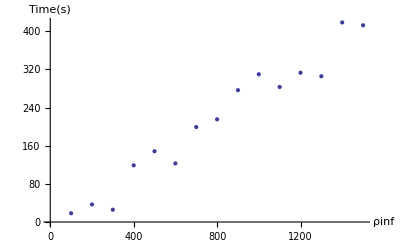

```mathematica
ListPlot[Table[{i*100,valtimes[[i,1]]},{i,1,15}],AxesLabel->{"ρinf","Time(s)"}]
```

### Values: Exponential!

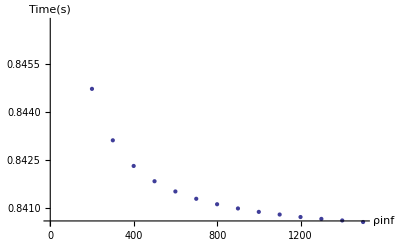

```mathematica
ListPlot[Table[{i*100,valtimes[[i,2]]},{i,1,15}],AxesLabel->{"ρinf","Time(s)"}]
```

### Checking asymtote:

```mathematica
(valtimes[[1,2]]-valtimes[[2,2]])-(valtimes[[2,2]]-valtimes[[4,2]])
```

0.00248474

```mathematica
(valtimes[[2,2]]-valtimes[[4,2]])-(valtimes[[4,2]]-valtimes[[8,2]])
```

0.00121582

```mathematica
(valtimes[[3,2]]-valtimes[[6,2]])-(valtimes[[6,2]]-valtimes[[12,2]])
```

0.000800781

### Fit?

I tried fitting it to an exponential just to see what would happen. It doesn’t seem that great?

```mathematica
FindFit[Table[valtimes[[i,2]],{i,1,15}],a*ⅇ^(-b x)+c,{a,b,c},x]
```

{a→0.0165017,b→0.658761,c→0.840877}

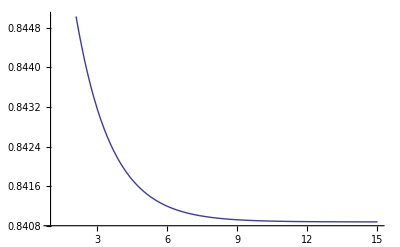

```mathematica
Plot[a*ⅇ^(-b x)+c/.{a->0.016501723385872448,b->0.6587607121172457,c->0.8408766180910944},{x,1,15}]
```

```mathematica
myFit=Table[a*ⅇ^(-b x)+c/.{a->0.016501723385872448,b->0.6587607121172457,c->0.8408766180910944},{x,1,15}];
```

```mathematica
Residuals=Table[myFit[[i]]-valtimes[[i,2]],{i,1,15}];
```

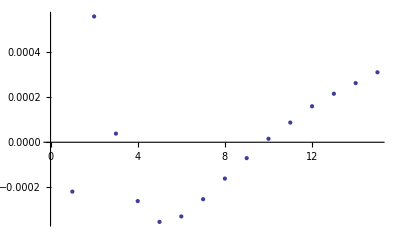

```mathematica
ListPlot[Residuals]
```

## Finding λcs

```mathematica
FindEigenvalues[λ_]:=Module[{H,dρ,ρinf,nn,vals,neg,i},
dρ=0.1;
ρinf=λ*50;
nn=Round[ρinf/dρ];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
vals=Sort[Eigenvalues[H,-100]];
neg=0;
For[i=1, vals[[i]]<0,i++,
neg++;
];
Print["Found eigenvalues for λ="<>ToString[λ]];
Return[{λ,vals[[1]],neg}]
]
```

```mathematica
FindSmallEigenvalues[λ_]:=Module[{H,dρ,ρinf,nn,vals,neg,i},
dρ=0.1;
ρinf=1000;
nn=Round[ρinf/dρ];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
vals=Sort[Eigenvalues[H,-100]];
neg=0;
For[i=1, vals[[i]]<0,i++,
neg++;
];
Print["Found eigenvalues for λ="<>ToString[λ]];
Return[{λ,vals[[1]],neg}]
]
```

### Using functions

```mathematica
FindEigenvalues[10]
```

Found eigenvalues for λ=10

{-0.811651,3}

```mathematica
λcs=Table[FindEigenvalues[λ],{λ,10,200,10}];
```

Found eigenvalues for λ=10

Found eigenvalues for λ=20

Found eigenvalues for λ=30

Found eigenvalues for λ=40

Found eigenvalues for λ=50

Found eigenvalues for λ=60

Found eigenvalues for λ=70

Found eigenvalues for λ=80

Found eigenvalues for λ=90

Found eigenvalues for λ=100

Found eigenvalues for λ=110

Found eigenvalues for λ=120

Found eigenvalues for λ=130

Found eigenvalues for λ=140

Found eigenvalues for λ=150

Found eigenvalues for λ=160

Found eigenvalues for λ=170

Found eigenvalues for λ=180

Found eigenvalues for λ=190

Found eigenvalues for λ=200

```mathematica
λcs
```

{{-0.811651,3},{-0.901151,4},{-0.93248,6},{-0.203397,5},{-0.212141,6},{-0.218117,7},{-0.0850855,7},{-0.0880685,7},{-0.0904388,8},{-0.0923671,9},{-0.0461494,8},{-0.0473794,9},{-0.0484379,9},{-0.0493581,10},{-0.0281947,9},{-0.028849,10},{-0.029435,10},{-0.0299627,10},{-0.0186106,10},{-0.0190094,10}}

```mathematica
For[i=4,i<Length[λcs],i++,
λcs[[i,2]]++;
]
```

```mathematica
λcs
```

{{-0.811651,3},{-0.901151,4},{-0.93248,6},{-0.203397,6},{-0.212141,7},{-0.218117,8},{-0.0850855,8},{-0.0880685,8},{-0.0904388,9},{-0.0923671,10},{-0.0461494,9},{-0.0473794,10},{-0.0484379,10},{-0.0493581,11},{-0.0281947,10},{-0.028849,11},{-0.029435,11},{-0.0299627,11},{-0.0186106,11},{-0.0190094,10}}

```mathematica
For[i=7,i<Length[λcs],i++,
λcs[[i,2]]++;
]
```

```mathematica
λcs
```

{{-0.811651,3},{-0.901151,4},{-0.93248,6},{-0.203397,6},{-0.212141,7},{-0.218117,8},{-0.0850855,9},{-0.0880685,9},{-0.0904388,10},{-0.0923671,11},{-0.0461494,10},{-0.0473794,11},{-0.0484379,11},{-0.0493581,12},{-0.0281947,11},{-0.028849,12},{-0.029435,12},{-0.0299627,12},{-0.0186106,12},{-0.0190094,10}}

```mathematica
λcs[[Length[λcs],2]]=λcs[[Length[λcs],2]]+2;
```

```mathematica
For[i=11,i<=Length[λcs],i++,
λcs[[i,2]]++;
]
```

```mathematica
λcs
```

{{-0.811651,3},{-0.901151,4},{-0.93248,6},{-0.203397,6},{-0.212141,7},{-0.218117,8},{-0.0850855,9},{-0.0880685,9},{-0.0904388,10},{-0.0923671,11},{-0.0461494,11},{-0.0473794,12},{-0.0484379,12},{-0.0493581,13},{-0.0281947,12},{-0.028849,13},{-0.029435,13},{-0.0299627,13},{-0.0186106,13},{-0.0190094,13}}

```mathematica
For[i=15,i<Length[λcs],i++,
λcs[[i,2]]++;
]
```

```mathematica
λcs
```

{{-0.811651,3},{-0.901151,4},{-0.93248,6},{-0.203397,6},{-0.212141,7},{-0.218117,8},{-0.0850855,9},{-0.0880685,9},{-0.0904388,10},{-0.0923671,11},{-0.0461494,11},{-0.0473794,12},{-0.0484379,12},{-0.0493581,13},{-0.0281947,13},{-0.028849,14},{-0.029435,14},{-0.0299627,14},{-0.0186106,14},{-0.0190094,13}}

```mathematica
For[i=19,i<Length[λcs],i++,
λcs[[i,2]]++;
]
```

```mathematica
λcs
```

{{-0.811651,3},{-0.901151,4},{-0.93248,6},{-0.203397,6},{-0.212141,7},{-0.218117,8},{-0.0850855,9},{-0.0880685,9},{-0.0904388,10},{-0.0923671,11},{-0.0461494,11},{-0.0473794,12},{-0.0484379,12},{-0.0493581,13},{-0.0281947,13},{-0.028849,14},{-0.029435,14},{-0.0299627,14},{-0.0186106,15},{-0.0190094,13}}

```mathematica
λcs[[Length[λcs],2]]=λcs[[Length[λcs],2]]+2;
```

```mathematica
λcs={{-0.8116509099286732,3},{-0.901151176645247,4},{-0.9324796536200184,6},{-0.20339714514592694,6},{-0.21214149589307435,7},{-0.21811734634504892,8},{-0.085085513430572,9},{-0.0880685358611549,9},{-0.09043877264731547,10},{-0.09236709359740117,11},{-0.04614937941245101,11},{-0.04737941098516268,12},{-0.048437853243728395,12},{-0.04935814265055546,13},{-0.028194725664643816,13},{-0.028849042073670842,14},{-0.029434995708949238,14},{-0.029962705059092196,14},{-0.018610558760733704,15},{-0.01900944246754701,15}}
```

{{-0.811651,3},{-0.901151,4},{-0.93248,6},{-0.203397,6},{-0.212141,7},{-0.218117,8},{-0.0850855,9},{-0.0880685,9},{-0.0904388,10},{-0.0923671,11},{-0.0461494,11},{-0.0473794,12},{-0.0484379,12},{-0.0493581,13},{-0.0281947,13},{-0.028849,14},{-0.029435,14},{-0.0299627,14},{-0.0186106,15},{-0.0190094,15}}

### No. of negative eigenvalues vs. λ, λ=10 through 200.

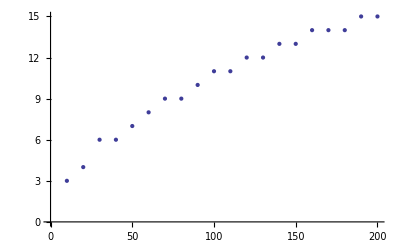

```mathematica
ListPlot[Table[{i*10,λcs[[i,2]]},{i,1,Length[λcs]}]]
```

### Look at this data. Just look at it.

```mathematica
finallcs={5,5,5,15,25,25,45,55,65,85,95,115,135,155,185}
```

{5,5,5,15,25,25,45,55,65,85,95,115,135,155,185}

```mathematica
FindFit[finallcs,a*x^2,a,x]
```

{a→0.808695}

```mathematica
shiny=Plot[a*x^2/.{a->0.808694871909911},{x,1,15}];
```

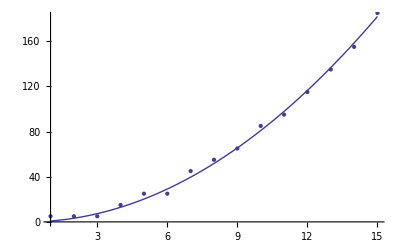

```mathematica
Show[shiny,ListPlot[finallcs]]
```

## More Detail

### The work

```mathematica
λcs=Table[FindEigenvalues[λ],{λ,10,200,10}];
```

Found eigenvalues for λ=10

Found eigenvalues for λ=20

Found eigenvalues for λ=30

Found eigenvalues for λ=40

Found eigenvalues for λ=50

Found eigenvalues for λ=60

Found eigenvalues for λ=70

Found eigenvalues for λ=80

Found eigenvalues for λ=90

Found eigenvalues for λ=100

Found eigenvalues for λ=110

Found eigenvalues for λ=120

Found eigenvalues for λ=130

Found eigenvalues for λ=140

Found eigenvalues for λ=150

Found eigenvalues for λ=160

Found eigenvalues for λ=170

Found eigenvalues for λ=180

Found eigenvalues for λ=190

Found eigenvalues for λ=200

```mathematica
λcs
```

{{10,-0.0997188,2},{20,-0.0386787,3},{30,-0.0170062,3},{40,-0.00804812,3},{50,-0.0120568,3},{60,-0.00609536,3},{70,-0.00802248,4},{80,-0.00429258,4},{90,-0.0022818,3},{100,-0.0029849,4},{110,-0.00162691,3},{120,-0.00207446,4},{130,-0.00114476,3},{140,-0.00144257,4},{150,-0.00173383,4},{160,-0.00100143,4},{170,-0.00120447,4},{180,-0.000691383,4},{190,-0.000835637,4},{200,-0.00097922,4}}

```mathematica
narrow=Table[FindEigenvalues[λ],{λ,90.,100.,1}];
```

Found eigenvalues for λ=90.

Found eigenvalues for λ=91.

Found eigenvalues for λ=92.

Found eigenvalues for λ=93.

Found eigenvalues for λ=94.

Found eigenvalues for λ=95.

Found eigenvalues for λ=96.

Found eigenvalues for λ=97.

Found eigenvalues for λ=98.

Found eigenvalues for λ=99.

Found eigenvalues for λ=100.

```mathematica
narrow
```

{{90.,-0.0022818,3},{91.,-0.00235366,3},{92.,-0.00242523,3},{93.,-0.00249648,3},{94.,-0.0025674,3},{95.,-0.00263796,3},{96.,-0.00270815,4},{97.,-0.00277795,4},{98.,-0.00284735,4},{99.,-0.00291634,4},{100.,-0.0029849,4}}

```mathematica
smλc=Table[FindSmallEigenvalues[λ],{λ,0.5,1.,0.1}];
```

Found eigenvalues for λ=0.5

$Aborted

```mathematica
smλc
```

{{1,-0.0198333,1},{2,9.89538×10^-6,0},{3,9.36573×10^-6,0},{4,-0.00673899,1},{5,-0.0241268,1},{6,-0.0427007,1},{7,-0.0598193,1},{8,-0.074953,2},{9,-0.088176,2},{10,-0.00640173,1}}

```mathematica
dρ=0.1;
ρinf=100;
nn=10000;
```

```mathematica
e0=Bisect2[Critical2,{0.1,1000,100000},0.7,0.9,10.0^(-6)]
```

Bisecting. Midpoint 0.8

Bisecting. Midpoint 0.85

Bisecting. Midpoint 0.825

Bisecting. Midpoint 0.8375

Bisecting. Midpoint 0.84375

Bisecting. Midpoint 0.840625

Bisecting. Midpoint 0.842188

Bisecting. Midpoint 0.842969

Bisecting. Midpoint 0.842578

Bisecting. Midpoint 0.842773

Bisecting. Midpoint 0.842676

Bisecting. Midpoint 0.842725

Bisecting. Midpoint 0.842749

Bisecting. Midpoint 0.842761

Bisecting. Midpoint 0.842767

Bisecting. Midpoint 0.84277

Bisecting. Midpoint 0.842772

Bisecting. Midpoint 0.842771

Bisecting. Midpoint 0.842771

0.842771

```mathematica
e1=Bisect2[Critical2,{0.1,1000,100000},2.9,3.4,10.0^(-6)]
```

Bisecting. Midpoint 3.15

Bisecting. Midpoint 3.275

Bisecting. Midpoint 3.2125

Bisecting. Midpoint 3.24375

Bisecting. Midpoint 3.22813

Bisecting. Midpoint 3.22031

Bisecting. Midpoint 3.22422

Bisecting. Midpoint 3.22617

Bisecting. Midpoint 3.22715

Bisecting. Midpoint 3.22764

Bisecting. Midpoint 3.22739

Bisecting. Midpoint 3.22727

Bisecting. Midpoint 3.22721

Bisecting. Midpoint 3.22724

Bisecting. Midpoint 3.22726

Bisecting. Midpoint 3.22726

Bisecting. Midpoint 3.22727

Bisecting. Midpoint 3.22727

Bisecting. Midpoint 3.22727

«1 more identical outputs»

3.22727

```mathematica
e2=Bisect2[Critical2,{0.1,1000,100000},7.,8.,10.0^(-6)]
```

Bisecting. Midpoint 7.5

Bisecting. Midpoint 7.25

Bisecting. Midpoint 7.125

Bisecting. Midpoint 7.1875

Bisecting. Midpoint 7.21875

Bisecting. Midpoint 7.20313

Bisecting. Midpoint 7.19531

Bisecting. Midpoint 7.19922

Bisecting. Midpoint 7.20117

Bisecting. Midpoint 7.20215

Bisecting. Midpoint 7.20166

Bisecting. Midpoint 7.2019

Bisecting. Midpoint 7.20178

Bisecting. Midpoint 7.20172

Bisecting. Midpoint 7.20169

Bisecting. Midpoint 7.20171

Bisecting. Midpoint 7.2017

Bisecting. Midpoint 7.2017

Bisecting. Midpoint 7.2017

«2 more identical outputs»

7.2017

```mathematica
e3=Bisect2[Critical2,{0.1,700,700/0.1},12.7,12.8,10.0^(-6)]
```

Bisecting. Midpoint 12.75

Bisecting. Midpoint 12.775

Bisecting. Midpoint 12.7875

Bisecting. Midpoint 12.7938

Bisecting. Midpoint 12.7906

Bisecting. Midpoint 12.7891

Bisecting. Midpoint 12.7883

Bisecting. Midpoint 12.7879

Bisecting. Midpoint 12.7881

Bisecting. Midpoint 12.7882

Bisecting. Midpoint 12.7881

Bisecting. Midpoint 12.7881

Bisecting. Midpoint 12.7881

«5 more identical outputs»

12.7881

```mathematica
e3p2=Bisect2[Critical2,{0.1,1000,1000/0.1},19.,20.,10.0^(-6)]
```

Bisecting. Midpoint 19.5

Bisecting. Midpoint 19.75

Bisecting. Midpoint 19.875

Bisecting. Midpoint 19.9375

Bisecting. Midpoint 19.9063

Bisecting. Midpoint 19.9219

Bisecting. Midpoint 19.9141

Bisecting. Midpoint 19.9102

Bisecting. Midpoint 19.9121

Bisecting. Midpoint 19.9111

Bisecting. Midpoint 19.9116

Bisecting. Midpoint 19.9114

Bisecting. Midpoint 19.9113

Bisecting. Midpoint 19.9113

Bisecting. Midpoint 19.9113

«6 more identical outputs»

19.9113

```mathematica
e4=Bisect2[Critical2,{0.1,1500,1500/0.1},25.,30.,10.0^(-6)]
```

Bisecting. Midpoint 25

Bisecting. Midpoint 55
--
2

Bisecting. Midpoint 115
---
 4

Bisecting. Midpoint 225
---
 8

Bisecting. Midpoint 455
---
16

Bisecting. Midpoint 915
---
32

Bisecting. Midpoint 1835
----
 64

Bisecting. Midpoint 3665
----
128

Bisecting. Midpoint 7325
----
256

Bisecting. Midpoint 14655
-----
 512

Bisecting. Midpoint 29305
-----
1024

Bisecting. Midpoint 58605
-----
2048

Bisecting. Midpoint 117205
------
 4096

Bisecting. Midpoint 234405
------
 8192

Bisecting. Midpoint 468815
------
16384

Bisecting. Midpoint 937625
------
32768

Bisecting. Midpoint 1875255
-------
 65536

Bisecting. Midpoint 3750505
-------
131072

Bisecting. Midpoint 7501015
-------
262144

Bisecting. Midpoint 15002025
--------
 524288

Bisecting. Midpoint 30004045
--------
1048576

Bisecting. Midpoint 60008085
--------
2097152

Bisecting. Midpoint 120016165
---------
 4194304

Bisecting. Midpoint 240032335
---------
 8388608

Bisecting. Midpoint 480064675
---------
16777216

28.6141

```mathematica
e5=Bisect2[Critical2,{0.1,2000,2000/0.1},35.,40.,10.0^(-6)]
```

Bisecting. Midpoint 35

Bisecting. Midpoint 75
--
2

Bisecting. Midpoint 155
---
 4

Bisecting. Midpoint 315
---
 8

Bisecting. Midpoint 625
---
16

Bisecting. Midpoint 1245
----
 32

Bisecting. Midpoint 2495
----
 64

Bisecting. Midpoint 4985
----
128

Bisecting. Midpoint 9975
----
256

Bisecting. Midpoint 19945
-----
 512

Bisecting. Midpoint 39895
-----
1024

Bisecting. Midpoint 79795
-----
2048

Bisecting. Midpoint 159585
------
 4096

Bisecting. Midpoint 319175
------
 8192

Bisecting. Midpoint 638355
------
16384

Bisecting. Midpoint 1276705
-------
 32768

Bisecting. Midpoint 2553415
-------
 65536

Bisecting. Midpoint 5106825
-------
131072

Bisecting. Midpoint 10213655
--------
 262144

Bisecting. Midpoint 20427305
--------
 524288

Bisecting. Midpoint 40854605
--------
1048576

Bisecting. Midpoint 81709205
--------
2097152

Bisecting. Midpoint 163418415
---------
 4194304

Bisecting. Midpoint 326836825
---------
 8388608

Bisecting. Midpoint 653673655
---------
16777216

38.962

```mathematica
e6=Bisect2[Critical2,{0.1,2500,2500/0.1},50.,51.,10.0^(-6)]
```

Bisecting. Midpoint 50.5

Bisecting. Midpoint 50.75

Bisecting. Midpoint 50.625

Bisecting. Midpoint 50.6875

Bisecting. Midpoint 50.6563

Bisecting. Midpoint 50.6719

Bisecting. Midpoint 50.6797

Bisecting. Midpoint 50.6758

Bisecting. Midpoint 50.6777

Bisecting. Midpoint 50.6768

Bisecting. Midpoint 50.6772

Bisecting. Midpoint 50.677

Bisecting. Midpoint 50.6769

Bisecting. Midpoint 50.6768

Bisecting. Midpoint 50.6768

Bisecting. Midpoint 50.6768

«5 more identical outputs»

50.6768

```mathematica
e7=Bisect2[Critical2,{0.1,3200,3200/0.1},64.,65.,10.0^(-6)]
```

Bisecting. Midpoint 64.5

Bisecting. Midpoint 64.25

Bisecting. Midpoint 64.125

Bisecting. Midpoint 64.0625

Bisecting. Midpoint 64.0938

Bisecting. Midpoint 64.0781

Bisecting. Midpoint 64.0703

Bisecting. Midpoint 64.0664

Bisecting. Midpoint 64.0684

Bisecting. Midpoint 64.0674

Bisecting. Midpoint 64.0679

Bisecting. Midpoint 64.0681

Bisecting. Midpoint 64.0682

Bisecting. Midpoint 64.0682

Bisecting. Midpoint 64.0682

«6 more identical outputs»

64.0682

```mathematica
e8=Bisect2[Critical2,{0.1,4000,4000/0.1},79.,80.,10.0^(-6)]
```

Bisecting. Midpoint 79.5

Bisecting. Midpoint 79.25

Bisecting. Midpoint 79.125

Bisecting. Midpoint 79.0625

Bisecting. Midpoint 79.0313

Bisecting. Midpoint 79.0156

Bisecting. Midpoint 79.0234

Bisecting. Midpoint 79.0273

Bisecting. Midpoint 79.0293

Bisecting. Midpoint 79.0283

Bisecting. Midpoint 79.0288

Bisecting. Midpoint 79.0291

Bisecting. Midpoint 79.0289

Bisecting. Midpoint 79.029

Bisecting. Midpoint 79.029

Bisecting. Midpoint 79.029

«5 more identical outputs»

79.029

```mathematica
e9=Bisect2[Critical2,{0.1,5000,5000/0.1},95.,96.,10.0^(-6)]
```

Bisecting. Midpoint 95.5

Bisecting. Midpoint 95.75

Bisecting. Midpoint 95.625

Bisecting. Midpoint 95.5625

Bisecting. Midpoint 95.5313

Bisecting. Midpoint 95.5469

Bisecting. Midpoint 95.5547

Bisecting. Midpoint 95.5508

Bisecting. Midpoint 95.5527

Bisecting. Midpoint 95.5518

Bisecting. Midpoint 95.5522

Bisecting. Midpoint 95.5525

Bisecting. Midpoint 95.5526

Bisecting. Midpoint 95.5526

Bisecting. Midpoint 95.5525

Bisecting. Midpoint 95.5525

Bisecting. Midpoint 95.5525

«4 more identical outputs»

95.5525

### Results

```mathematica
lambdas={0.8427707672119141,3.2272700309753417,7.20170259475708,12.78813133239746,19.911264896392822,28.61408442258835,38.961986005306244,50.67683267593384,64.06821012496948,79.02897024154663,95.55251264572144}
```

{0.842771,3.22727,7.2017,12.7881,19.9113,28.6141,38.962,50.6768,64.0682,79.029,95.5525}

```mathematica
FindFit[lambdas,a*x^2,a,x]
```

{a→0.790959}

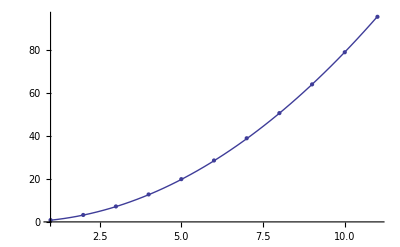

```mathematica
Show[Plot[a*x^2/.{a->0.7909590388030853},{x,1,Length[lambdas]}],ListPlot[lambdas]]
```

```mathematica
res=Table[(a*x^2/.{a->0.7955952205828261})-lambdas[[x]],{x,1,Length[lambdas]}]
```

{-0.0471755,-0.0448891,-0.0413456,-0.0586078,-0.0213844,0.0273435,0.0221798,0.241261,0.375003,0.530552,0.714509}

```mathematica
stuff=Table[(a*x^2/.{a->0.7955952205828261}),{x,1,Length[lambdas]}]
```

{0.795595,3.18238,7.16036,12.7295,19.8899,28.6414,38.9842,50.9181,64.4432,79.5595,96.267}

```mathematica
err=Table[Abs[res[[i]]]/stuff[[i]],{i,1,Length[lambdas]}]
```

{0.0592959,0.0141055,0.00577424,0.00460408,0.00107514,0.000954684,0.000568944,0.00473823,0.00581912,0.00666861,0.00742216}

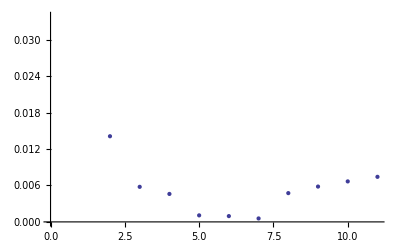

```mathematica
ListPlot[err]
```

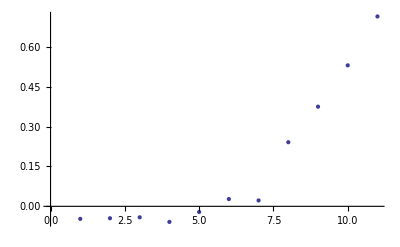

```mathematica
ListPlot[res]
```

```mathematica
Mean[res]
```

0.193114

## Low Eigenvalues

```mathematica
ls={3.2272700309753417,7.20170259475708};
```

```mathematica
DistributeDefinitions[Bisect2,Critical2,CountNegs,ls]
```

{Bisect2,CountNegs,Critical2,ls}

```mathematica
ParallelTable[{i,Bisect2[Critical2,{0.1,1000.*2^(j-1),1000.*2^(j-1)/0.1},ls[[i]]-1,ls[[i]]+1,10^(-6)]},{i,1,2},{j,1,3}]
```

Bisecting. Midpoint 3.22727

Bisecting. Midpoint 7.2017

Bisecting. Midpoint 7.7017

Bisecting. Midpoint 3.72727

Bisecting. Midpoint 3.47727

Bisecting. Midpoint 7.4517

Bisecting. Midpoint 3.35227

Bisecting. Midpoint 7.3267

Bisecting. Midpoint 3.28977

Bisecting. Midpoint 7.2642

Bisecting. Midpoint 3.25852

Bisecting. Midpoint 7.23295

Bisecting. Midpoint 3.2429

Bisecting. Midpoint 7.21733

Bisecting. Midpoint 3.23508

Bisecting. Midpoint 7.20952

Bisecting. Midpoint 3.23118

Bisecting. Midpoint 7.20561

Bisecting. Midpoint 3.23313

Bisecting. Midpoint 7.20366

Bisecting. Midpoint 3.23411

Bisecting. Midpoint 7.20268

Bisecting. Midpoint 3.23459

Bisecting. Midpoint 7.20219

Bisecting. Midpoint 3.23435

Bisecting. Midpoint 7.20195

Bisecting. Midpoint 3.23447

Bisecting. Midpoint 7.20182

Bisecting. Midpoint 3.23441

Bisecting. Midpoint 7.20176

Bisecting. Midpoint 3.23444

Bisecting. Midpoint 7.20173

Bisecting. Midpoint 3.23446

Bisecting. Midpoint 7.20172

Bisecting. Midpoint 3.23445

Bisecting. Midpoint 7.20171

Bisecting. Midpoint 3.23445

Bisecting. Midpoint 7.20171

Bisecting. Midpoint 3.23444

Bisecting. Midpoint 7.2017

Bisecting. Midpoint 3.23444

Bisecting. Midpoint 7.2017

Bisecting. Midpoint 3.23444

Bisecting. Midpoint 7.2017

Bisecting. Midpoint 3.22727

Bisecting. Midpoint 7.2017

Bisecting. Midpoint 3.72727

Bisecting. Midpoint 6.7017

Bisecting. Midpoint 3.47727

Bisecting. Midpoint 6.9517

Bisecting. Midpoint 3.35227

Bisecting. Midpoint 7.0767

Bisecting. Midpoint 3.28977

Bisecting. Midpoint 7.1392

Bisecting. Midpoint 3.25852

Bisecting. Midpoint 7.17045

Bisecting. Midpoint 3.2429

Bisecting. Midpoint 7.18608

Bisecting. Midpoint 3.23508

Bisecting. Midpoint 7.19389

Bisecting. Midpoint 3.23118

Bisecting. Midpoint 7.18998

Bisecting. Midpoint 3.22922

Bisecting. Midpoint 7.18803

Bisecting. Midpoint 3.2302

Bisecting. Midpoint 7.18705

Bisecting. Midpoint 3.23069

Bisecting. Midpoint 7.18754

Bisecting. Midpoint 3.23044

Bisecting. Midpoint 7.18779

Bisecting. Midpoint 3.23057

Bisecting. Midpoint 7.18766

Bisecting. Midpoint 3.2305

Bisecting. Midpoint 7.1876

Bisecting. Midpoint 3.23047

Bisecting. Midpoint 7.18763

Bisecting. Midpoint 3.23046

Bisecting. Midpoint 7.18765

Bisecting. Midpoint 3.23045

Bisecting. Midpoint 7.18764

Bisecting. Midpoint 3.23045

Bisecting. Midpoint 7.18765

Bisecting. Midpoint 3.23045

Bisecting. Midpoint 7.18764

Bisecting. Midpoint 3.23044

Bisecting. Midpoint 7.18764

Bisecting. Midpoint 3.23045

Bisecting. Midpoint 7.18764

Bisecting. Midpoint 3.22727

Bisecting. Midpoint 7.2017

Bisecting. Midpoint 6.7017

Bisecting. Midpoint 3.72727

Bisecting. Midpoint 6.9517

Bisecting. Midpoint 3.47727

Bisecting. Midpoint 7.0767

Bisecting. Midpoint 3.35227

Bisecting. Midpoint 7.1392

Bisecting. Midpoint 3.28977

Bisecting. Midpoint 7.17045

Bisecting. Midpoint 3.25852

Bisecting. Midpoint 7.18608

Bisecting. Midpoint 3.2429

Bisecting. Midpoint 7.17827

Bisecting. Midpoint 3.23508

Bisecting. Midpoint 7.18217

Bisecting. Midpoint 3.23118

Bisecting. Midpoint 7.18022

Bisecting. Midpoint 7.18119

Bisecting. Midpoint 3.22922

Bisecting. Midpoint 7.18071

Bisecting. Midpoint 3.22825

Bisecting. Midpoint 7.18095

Bisecting. Midpoint 3.22873

Bisecting. Midpoint 7.18083

Bisecting. Midpoint 3.22849

Bisecting. Midpoint 7.18077

Bisecting. Midpoint 3.22837

Bisecting. Midpoint 7.18074

Bisecting. Midpoint 3.22843

Bisecting. Midpoint 7.18072

Bisecting. Midpoint 3.22846

Bisecting. Midpoint 7.18073

Bisecting. Midpoint 7.18073

Bisecting. Midpoint 3.22844

Bisecting. Midpoint 7.18073

Bisecting. Midpoint 3.22845

Bisecting. Midpoint 7.18073

Bisecting. Midpoint 3.22846

Bisecting. Midpoint 7.18073

Bisecting. Midpoint 3.22846

Bisecting. Midpoint 3.22846

Bisecting. Midpoint 3.22846

{{{1,3.23444},{1,3.23045},{1,3.22846}},{{2,7.2017},{2,7.18764},{2,7.18073}}}

```mathematica
lls={{{1,3.2344430923461918},{1,3.2304452896118168},{1,3.228457832336426}},{{2,7.201703071594238},{2,7.187644004821777},{2,7.180727005004883}}};
```

```mathematica
lls=Flatten[lls,1]
```

{{1,3.23444},{1,3.23045},{1,3.22846},{2,7.2017},{2,7.18764},{2,7.18073}}